```mathematica
ClearAll["Global`*"]

$Assumptions=v∈Reals&&v>0&&τ∈Reals&&τ>0&&ξ∈Reals&&ξ>0&&l∈Reals&&r∈Reals;α[r_,ξ_]:=(1/2)*KroneckerDelta[0,Abs[-r]]-(1/4)*KroneckerDelta[1,Abs[-r]]+Exp[-(-r)^2/(8 π ξ^2)]/(2 Sqrt[2] π ξ) 
β[r_,τQ_,ξhat_,l_]:=Sign[-r]*((1/4) KroneckerDelta[1,Abs[-r]]-Exp[I*(2 τQ-Abs[-r]^2/(4 ξhat*l))]/(2 Sqrt[π] ξhat*l)*Exp[-π Abs[-r]^2/(4 l^2)]*Sqrt[1-Exp[-π Abs[-r]^2/(4 l^2)]]) 
βc[r_,τQ_,ξhat_,l_]:=Sign[-r]*((1/4) KroneckerDelta[1,Abs[-r]]-Exp[-I*(2 τQ-Abs[-r]^2/(4 ξhat*l))]/(2 Sqrt[π] ξhat*l)*Exp[-π Abs[-r]^2/(4 l^2)]*Sqrt[1-Exp[-π Abs[-r]^2/(4 l^2)]]) 
τ=1/v;l=Sqrt[τ]*Log[τ];ξ=Sqrt[τ];
```

```mathematica
AB[r_] := 2*α[r,ξ]+(β[r,τ,ξ,l]+βc[r,τ,ξ,l])-KroneckerDelta[0,r];
BA[r_] := KroneckerDelta[0,r]-2*α[r,ξ]-(β[r,τ,ξ,l]+βc[r,τ,ξ,l])
```

```mathematica
G[n_]:=BA[n-1]
```

```mathematica
Expand[Simplify[G[2]]]
```

1-(ⅇ^(-v/(8 π)) √v)/(√2 π)+(ⅇ^(-(2 ⅈ)/v-(π v)/(4 Log[v]^2)-(ⅈ v)/(4 Log[v])) √(1-ⅇ^(-(π v)/(4 Log[v]^2))) v)/(2 √π Log[v])+(ⅇ^((2 ⅈ)/v-(π v)/(4 Log[v]^2)+(ⅈ v)/(4 Log[v])) √(1-ⅇ^(-(π v)/(4 Log[v]^2))) v)/(2 √π Log[v])

```mathematica
sigmaGeneral[indices_List]:=Module[{removeDuplicatesInPairs,sorted,filtered,oddSites,evenSites,JWstringLengths,N,R={},Acoords,Bcoords,C},(*Remove pairs of duplicates:σ.b2=1*)removeDuplicatesInPairs[vec_List]:=Module[{tally=Tally[vec]},Flatten@Map[ConstantArray[#[[1]],Mod[#[[2]],2]]&,tally]];
sorted=Sort[indices];
filtered=removeDuplicatesInPairs[sorted];
(*sanity check*)If[Mod[Length[filtered],2]!=0,Return[0]];
oddSites=filtered[[1;; ;;2]];
evenSites=filtered[[2;; ;;2]];
JWstringLengths=evenSites-oddSites;
N=Total[JWstringLengths];
Do[R=Join[R,Range[filtered[[i]],filtered[[i+1]]]],{i,1,Length[filtered],2}];
Acoords=Complement[R,oddSites];
Bcoords=Complement[R,evenSites];
C=Table[With[{Nd=Acoords[[nx]]-Bcoords[[ny]]+1},G[Nd]],{nx,Length[Bcoords]},{ny,Length[Acoords]}];
Det[C]]
```

```mathematica
allCombinations[indices_List]:=Flatten[Table[Subsets[indices,{r}],{r,1,Length[indices]}],1];
Pn[n_Integer,even_:True]:=Module[{indices,terms,xc,counter,vecs,counts,dat={},relIndices,degen,shifted,val},indices=Range[0,n-1];
terms=allCombinations[indices];
(*normalize by subtracting first element*)xc=Map[#-First[#]&,terms];
(*remove empty list if present*)xc=DeleteCases[xc,{}];
(*group by relative structure and count degeneracies*)counter=Tally[xc];
vecs=counter[[All,1]];
counts=counter[[All,2]];
(*loop over terms*)Do[relIndices=vecs[[term]];
degen=counts[[term]];
If[OddQ[Length[relIndices]],If[even,AppendTo[dat,0],shifted=Join[relIndices,relIndices+Floor[n/2]];
val=sigmaGeneral[shifted];
AppendTo[dat,Sqrt[Abs[val]]*degen]],val=sigmaGeneral[relIndices];
AppendTo[dat,val*degen]],{term,Length[vecs]}];
AppendTo[dat,1];(*identity contribution*)N[Total[dat]/2^n]]
```

-(√v)/(√2 π)+(r^2 v^(3/2))/(8 √2 π^2)+((ⅇ^((2 ⅈ)/v-(r^2 v (π-ⅈ Log[v]))/(4 Log[v]^2))+ⅇ^(-(2 ⅈ)/v-(r^2 v (π+ⅈ Log[v]))/(4 Log[v]^2))) v^(3/2) Abs[r] Sign[r])/(4 Abs[Log[v]] Log[v])+1/2 (2 0,r-2 0,Abs[r]+1,Abs[r]+1,Abs[r] Sign[r])

1/(√2 π √τ)

1/2+ⅇ^(-π τ) BesselI[0,π τ]

1/(√2 π √τ)

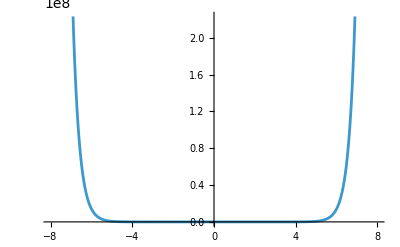

```mathematica
Normal[Series[Simplify[BA[r]],{v,0,2}]]
```

```mathematica
A = {{1, Cos[Δ]/2}}
```